```mathematica
data=FinancialData["^OEX","Close",{"Jan. 2, 1986","Dec. 19, 1989"}];
```

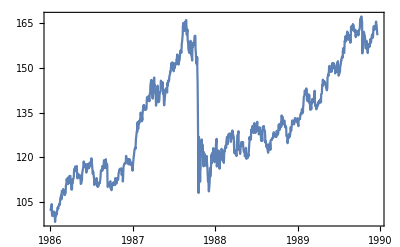

```mathematica
DateListPlot[data]
```

```mathematica
Last@data
```

{{1989,12,19},161.03}

```mathematica
Subscript[α, 0]=1.524*^-5;
Subscript[α, 1]=0.1883;
Subscript[β, 1]=0.7162;
λ=7.452*^-3;
r=0;
```

```mathematica
n=CDF[NormalDistribution[],#]&;
```

```mathematica
σ=√(Subscript[α, 0]/(1-Subscript[α, 1]-Subscript[β, 1]));
```

```mathematica
d[X_,K_,T_]:=(Log[X/K]+(r+σ^2/2)T)/(σ √T);
```

```mathematica
call[X_,K_,T_]:=With[{d=d[X,K,T]},X n[d]-Exp[-T r]K n[d-σ √T]];
delta[X_,K_,T_]:=n[d[X,K,T]];
SetAttributes[#,Listable]&/@{call,delta};
```

```mathematica
K=1.;
```

```mathematica
T=30;
```

```mathematica
sx={0.8,0.9,0.95,1,1.05,1.10,1.20};
```

```mathematica
prices=call[sx,K,T]*10000
```

{0.104397,18.2536,89.7605,275.978,600.387,1027.94,2000.99}

```mathematica
deltas=delta[sx,K,T]
```

{0.000710311,0.0683561,0.239867,0.513799,0.770273,0.921037,0.996203}

```mathematica
Transpose[{sx,NumberForm[#,{∞,4}]&/@prices}]//TableForm
```

0.8 | 0.1044
0.9 | 18.2536
0.95 | 89.7605
1 | 275.9783
1.05 | 600.3870
1.1 | 1027.9448
1.2 | 2000.9914

```mathematica
Transpose[{sx,NumberForm[#,{4,4}]&/@deltas}]//TableForm
```

0.8 | 0.0007
0.9 | 0.0684
0.95 | 0.2399
1 | 0.5138
1.05 | 0.7703
1.1 | 0.9210
1.2 | 0.9962

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 1, "Expiration"->30/365},  {"InterestRate"-> 0, "Volatility" -> √365 σ, "CurrentPrice"-> 0.8}]*10000
```

0.104397

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 1, "Expiration"->30/365,"Value"->0.1027/10000},  {"InterestRate"-> 0, "CurrentPrice"-> 0.8},"ImpliedVolatility"]
```

0.241041